#### Mathematica file to compute New Physics contributions to g-2. Acknowledgments should be referred to: Farinaldo S. Queiroz and William Shepherd [arxiv:1403.2309] and M Lindner, M Platscher, FS Queiroz, e-Print: 1610.06587v2, [hep-ph]• DOI: 10.1016/j.physrep.2017.12.001 A. S. de Jesus, S. Kovalenko, C. A. de S. Pires, F. S. Queiroz, and Y. S. Villamizar Phys. Lett. B, vol. 809, p. 135689, 2020. e-Print: 2003.06440 [hep-ph]•DOI: 10.1016/j.physletb.2020.135689 (publication) M. Lindner, M. Platscher, and F. S. Queiroz Phys. Rept. vol. 731, pp. 1-82, 2018. e-Print: 1610.06587 • DOI: 10.1016/j.physrep.2017.12.001 Yoxara S. Villamizar, Farinaldo S. Queiroz, Alvaro S. de Jesus, Sergey Kovalenko, and C. A. de S. Pires. Implications of the Muon Anomalous Magnetic Moment for 3-3-1 Models. PoS EPS-HEP2021 (2022) 638 • DOI: 10.22323/1.398.0638 (publication)

The reader should straightforwardly use this mathematica file to compute the total contribution of a generic model to the muon magnetic moment at 1-loop level. Plots are also available. We have closely followed the notation of our paper arxiv:

New Physics Contribution to (g-2)_μ

## 3-3-1 LHN M_N = 240GeV

Global Parameters. 
Masses of the SM particles in GeV units.

```mathematica
mμ=0.105; (*Muon mass*)  mν=0.1*10^-9; (*Neutrino mass*) Mw=80; (*W boson mass*) MZ=90;(*Z mass*)Mh=125; (*Higgs mass*)
v=246; g=0.65;veta=174; vrho=Sqrt[246^2-veta^2]; λ2=0.1;λ6=0.1;mN=240;
```

Experimental Bounds
based on:
Current Bound: (261 ± 78) x 10^-11;
Projected 1 sigma bound < 34 x 10^-11;

```mathematica
BoundCurrenteup=Table[{x,339*10^-11},{x,1,10000,1}];
BoundCurrentdown=Table[{x,183*10^-11},{x,1,10000,1}];
sigmaCurrent=Table[{x,78*10^-11},{x,1,10000,1}];
sigmaProjected=Table[{x,34*10^-11},{x,1,10000,1}];
```

## 1. Neutral scalar (S2)

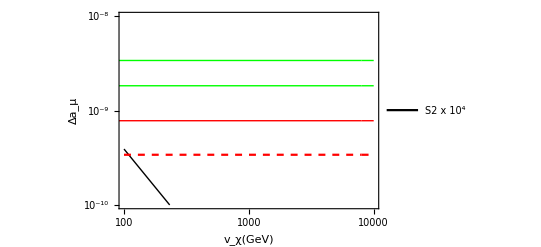

```mathematica
mf1:=mμ;ϵ1:=mf1/mμ;
MS2=√(1/2 (2 veta^2 (2 λ2-λ6)+Vqui^2));
λ1:=mμ/MS2;gs1:=(√2 mμ)/(2 vrho);gp1:=0;
ΔaNeutralScalar=Table[{Vqui,((gp1^2 mμ^2) NIntegrate[(x^2 (-x-ϵ1+1))/((1-x) (1-λ1^2 x)+λ1^2 x ϵ1^2),{x,0,1}])/(2 (4 π^2 MS2^2))+((gs1^2 mμ^2) NIntegrate[(x^2 (-x+ϵ1+1))/((1-x) (1-λ1^2 x)+λ1^2 x ϵ1^2),{x,0,1}])/(2 (4 π^2 MS2^2))},{Vqui,100,10000,500}];
size1=Dimensions[ΔaNeutralScalar];
ΔaNeutralScalarnew=Table[{ΔaNeutralScalar⟦i,1⟧,10^4 ΔaNeutralScalar⟦i,2⟧},{i,1,size1⟦1⟧}];
ListLogLogPlot[{ΔaNeutralScalarnew,BoundCurrenteup,BoundCurrentdown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{1/10^10,1/10^8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v, χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa, μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"S2 x 10⁴"}],{0.8,0.9}]]
```

### 2. Charged Scalar h_2

L ~ gs2 h^+ ν̄ μ + i gp2  h^+ ν̄ γ^5 μ  

Note: the difference between the Section 2.1 and 2.2 is the conjugation matrix. They lead to the same result. Therefore the result below applies to both.

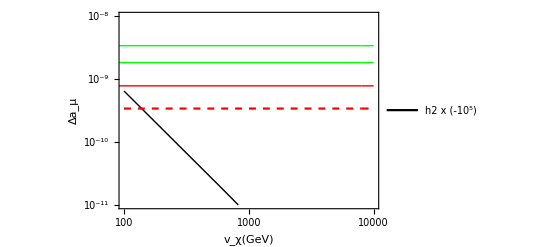

```mathematica
λ8=1;Mhp=Sqrt[(Vqui^2/2) + (λ8*v)];
mf2:=mν;ϵ2:=mf2/mμ;λ2:=mμ/Mhp;gs2:=mμ*Sqrt[2]/veta;gp2:=mμ*Sqrt[2]/veta;
ΔaChargedScalar1=Table[{Vqui,(-gs2^2*mμ^2)/(4*π^2*Mhp^2)*(1/2*NIntegrate[(x*(1-x)*(x+ϵ2))/(ϵ2^2*λ2^2*(1-x)*(1-ϵ2^-2*x)+x),{x,0,1}])+(-gp2^2*mμ^2)/(4*π^2*Mhp^2)*(1/2*NIntegrate[(x*(1-x)*(x-ϵ2))/(ϵ2^2*λ2^2*(1-x)*(1-ϵ2^-2*x)+x),{x,0,1}])},{Vqui,100,10000,500}];size2=Dimensions[ΔaChargedScalar1];
ΔaChargedScalar1new=Table[{ΔaChargedScalar1[[i,1]],-ΔaChargedScalar1[[i,2]]*10^5},{i,1,size2[[1]]}];

ListLogLogPlot[{ΔaChargedScalar1new,BoundCurrenteup,BoundCurrentdown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-11,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"h2 x (-10⁵)"}],{0.7,0.9}]]
```

#### 3. Charged -Scalar h_1

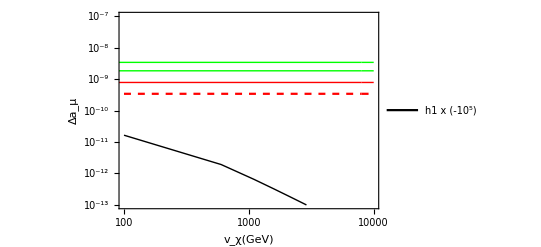

```mathematica
λ9=1;Mhp2=√(1/2 (λ9+1/2) (vrho^2+Vqui^2));
mf2:=mN;ϵ2:=mf2/mμ;λ2:=mμ/Mhp2;gs2:=(mμ √2)/(2 veta);gp2:=(mμ √2)/(2 veta);
ΔaChargedScalar2=Table[{Mhp2,-((gs2^2 mμ^2) NIntegrate[(x (1-x) (x+ϵ2))/(ϵ2^2 λ2^2 (1-x) (1-x/ϵ2^2)+x),{x,0,1}])/((4 π^2 Mhp2^2) 2)-((gp2^2 mμ^2) NIntegrate[(x (1-x) (x-ϵ2))/(ϵ2^2 λ2^2 (1-x) (1-x/ϵ2^2)+x),{x,0,1}])/((4 π^2 Mhp2^2) 2)},{Mhp2,100,10000,500}];
size10=Dimensions[ΔaChargedScalar2];
ΔaChargedScalar2new=Table[{ΔaChargedScalar2⟦i,1⟧,-ΔaChargedScalar2⟦i,2⟧ 10^5},{i,1,size10⟦1⟧}];
ListLogLogPlot[{ΔaChargedScalar2new,BoundCurrenteup,BoundCurrentdown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{1/10^13,1/10^7}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v, χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa, μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"h1 x (-10⁵)"}],{0.7,0.9}]]
```

#### 4. Z’ boson

L ~ gv9 Z' μ̄ γ^μ μ +  ga9 Z' μ̄ γ^μγ^5 μ

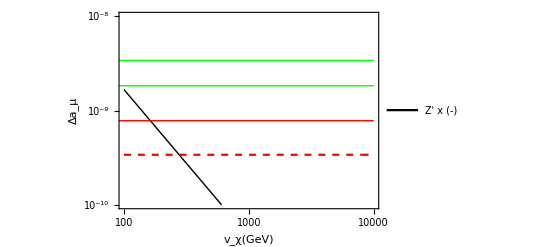

```mathematica
sw2=0.231;cw=Sqrt[1-sw2];
gp=g*Sqrt[sw2]/cw;
MZp=Sqrt[g^2/(4*(3-4sw2))*(4*Vqui^2+vrho^2/cw^2+veta^2*(1-2*sw2)^2/cw^2)];
mf9=mμ; ϵ9=mf9/mμ;λ9=mμ/MZp;gv9=(g*(1-4*sw2))/(cw*4*Sqrt[3-4 sw2]);ga9=g/(cw*4*Sqrt[3-4 sw2]);
ΔaZp=Table[{Vqui,(gv9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2+2ϵ9)+λ9^2*(1-ϵ9)^2*x^2*(1+ϵ9-x))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] 
+ (ga9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2-2ϵ9)+λ9^2*(1+ϵ9)^2*x^2*(1-ϵ9-x))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] },{Vqui,100,10000,500}];
size3=Dimensions[ΔaZp];
ΔaZpnew=Table[{ΔaZp[[i,1]],-ΔaZp[[i,2]]},{i,1,size3[[1]]}];ListLogLogPlot[{ΔaZpnew,BoundCurrenteup,BoundCurrentdown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"Z' x (-)"}],{0.5,0.2}]]
```

#### 5. Charged Vector Boson

L ~ gv10 W_μ^('+)ν̄ γ^μ μ + ga10 W_μ^('+)ν̄ γ^μγ^5 μ.  The sort ot interactions of Eq.8 in our manuscript give rise to the same contribution below.

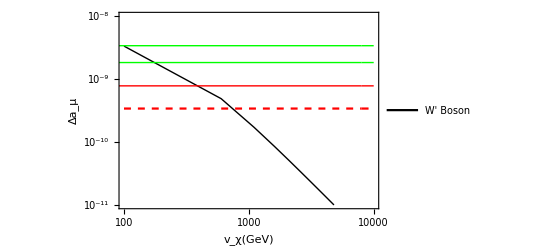

```mathematica
MWp=Sqrt[g^2/4*(veta^2+Vqui^2)];
ϵ10=mN/mμ; λ10=mμ/MWp;gv10=g/(2*Sqrt[2]);ga10=g/(2*Sqrt[2]);
ΔaChargedVec=Table[{Vqui,-(gv10^2*mμ^2)/(8*π^2*MWp^2)*NIntegrate[(-2*x^2*(1+x-2*ϵ10)+λ10^2*(1-ϵ10)^2*x*(1-x)*(x+ϵ10))/(ϵ10^2*λ10^2*(1-x)*(1-ϵ10^-2*x)+x),{x,0,1}]+-(ga10^2*mμ^2)/(8*π^2*MWp^2)*NIntegrate[(-2*x^2*(1+x+2*ϵ10)+λ10^2*(1+ϵ10)^2*x*(1-x)*(x-ϵ10))/(ϵ10^2*λ10^2*(1-x)*(1-ϵ10^-2*x)+x),{x,0,1}]},{Vqui,100,10000,500}];
size100=Dimensions[ΔaChargedVec];
ΔaChargedVecnew=Table[{ΔaChargedVec[[i,1]],ΔaChargedVec[[i,2]]},{i,1,size100[[1]]}];
plot10=ListLogLogPlot[{ΔaChargedVec,BoundCurrenteup,BoundCurrentdown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-11,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"W' Boson"}],{0.5,0.2}]]
```

COMBINED CONTRIBUTIONS

```mathematica
plottotal1=ListLogLogPlot[{ΔaChargedScalar1new,ΔaChargedScalar2new,ΔaNeutralScalarnew,ΔaChargedVec,ΔaZpnew,BoundCurrenteup,sigmaCurrent,sigmaProjected,BoundCurrentdown},PlotStyle->{Directive[Black,Dashed],Directive[Yellow,Dashed],Directive[Purple,Thick],Directive[Blue,Thick],Directive[Gray,Dashed],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick]},Joined->True,PlotRange->{{100,4000},{10^-11,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"h_2^+ x (-10^5)","h_1^+ x (-10^5)","S_2 x (10^4)","W'^+","Z ' x (-1)","Δa_μ Current"}],PlotLabel->Style["3-3-1  LHN",14, Black,Bold]]
```

```mathematica
sizetotal=Dimensions[ΔaChargedScalar1];
sizetotal[[1]]

Totalcontri=
Table[{ΔaChargedScalar1[[i,1]],ΔaChargedScalar1[[i,2]]+ΔaChargedScalar2[[i,2]]+ΔaNeutralScalar[[i,2]]+ΔaZp[[i,2]]+ΔaChargedVec[[i,2]]},{i,1,sizetotal[[1]]}];
```

20

```mathematica
plottotal2=ListLogLogPlot[{Totalcontri,BoundCurrenteup,sigmaCurrent,sigmaProjected,BoundCurrentdown},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick]},Joined->True,PlotRange->{{100,2000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"Total","Δa_μ Current","Δa_μ Projected"}],PlotLabel->Style["3-3-1  LHN",14, Black,Bold]]
```